# 配色

```mathematica
Huee[x_]:=Hue[0.7x]
```

```mathematica
Argg[x_]:=Piecewise[{{Arg[x],Arg[x]>0},{Arg[x]+2Pi,Arg[x]<0}}]
```

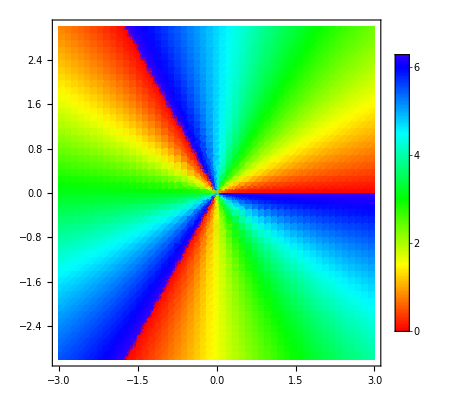

```mathematica
DensityPlot[Argg[(x+I y)]*3//Mod[#,2Pi]&,{x,-3,3},{y,-3,3},ColorFunction->(Huee[#/2/Pi]&),ColorFunctionScaling->False,PlotPoints->50,PlotLegends->Automatic]
```

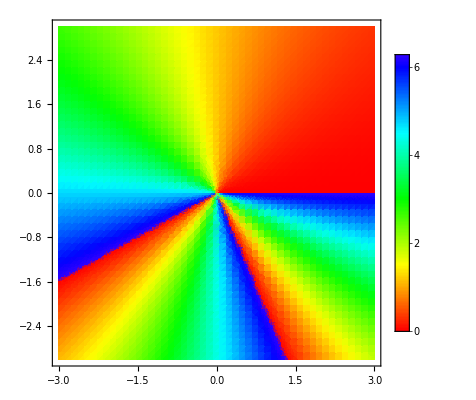

```mathematica
DensityPlot[((Argg[x+I y]/2/Pi)^2*6Pi)//Mod[#,2Pi]&,{x,-3,3},{y,-3,3},ColorFunction->(Huee[#/2/Pi]&),ColorFunctionScaling->False,PlotPoints->50,PlotLegends->Automatic]
```

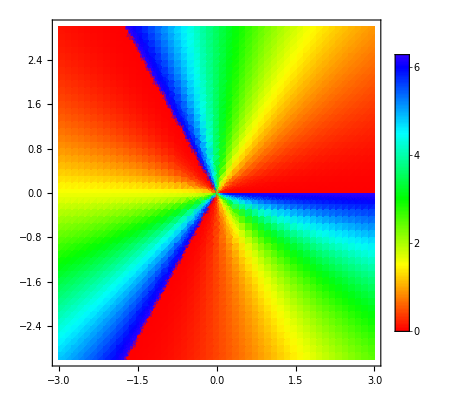

```mathematica
DensityPlot[(2Pi (Mod[3 Argg[x+I y],2Pi]/2/Pi)^2)//Mod[#,2Pi]&,{x,-3,3},{y,-3,3},ColorFunction->(Huee[#/2/Pi]&),ColorFunctionScaling->False,PlotPoints->50,PlotLegends->Automatic]
```

### 公式12

```mathematica
EE[ρ_,θ_,z_]:=(I/(2λ z R1))*Exp[-I k ρ^2/2/z]*(Exp[-k^2*ρ^2] M0+Sum[Sum[Gamma[ρ+l/2+1]/(p! Gamma[p+l+1])*(-k^2*ρ^2/(4z^2 R1))^(p+l/2),{p,0,Infinity}],{l,1,Infinity}]*(Exp[-I l θ]*Ml+Exp[I l θ]*Ml1))
```

```mathematica
EE[ρ,θ,z]
```

1/(2 R1 z λ)ⅈ ⅇ^(-(ⅈ k ρ^2)/(2 z)) (ⅇ^(-k^2 ρ^2) M0+(ⅇ^(-ⅈ l θ) Ml+ⅇ^(ⅈ l θ) Ml1) ∑_(l=1)^∞ ((k ρ)/(√R1 z))^-l (-(k^2 ρ^2)/(R1 z^2))^(l/2) BesselJ[l,(k ρ)/(√R1 z)] Gamma[1/2 (2+l+2 ρ)])

```mathematica
EE[1,Pi/2,1]
```

1/(2 R1 λ)ⅈ ⅇ^(-(ⅈ k)/2) (ⅇ^(-k^2) M0+(ⅇ^(-1/2 ⅈ l π) Ml+ⅇ^((ⅈ l π)/2) Ml1) ∑_(l=1)^∞ (-k^2/R1)^(l/2) (k/(√R1))^-l BesselJ[l,k/(√R1)] Gamma[(4+l)/2])

### 公式14

```mathematica
EEE[x_,y_,z_]:=InverseFunction[F][F[A0*Exp[-(x^2+y^2)/w^2]]*Exp[I 2Pi (Mod[m ϕ,2Pi]/2Pi)^n]*Exp[I (ωx^2+ωy^2)*z/(2k)]]*Exp[-I k z]
```

```mathematica
EEE[1,2,2]
```

ⅇ^(-2 ⅈ k) F^(-1)[ⅇ^((ⅈ (ωx^2+ωy^2))/k+ⅈ 2^(1-n) π^(1+n) Mod[m ϕ,2 π]^n) F[A0 ⅇ^(-5/w^2)]]